## Import Music Data & Flatten Music

```mathematica
bluesData = Import["/Users/armpa/Downloads/Compressed/genres/blues/*.wav"];
flatBlues = Flatten[AudioSplit[#,15] & /@ bluesData];
```

```mathematica
classicalData = Import["/Users/armpa/Downloads/Compressed/genres/classical/*.wav"];
flatClassical = Flatten[AudioSplit[#,15] & /@ classicalData];
```

```mathematica
countryData = Import["/Users/armpa/Downloads/Compressed/genres/country/*.wav"];
flatCountry = Flatten[AudioSplit[#,15] & /@ countryData];
```

```mathematica
discoData = Import["/Users/armpa/Downloads/Compressed/genres/disco/*.wav"];
flatDisco = Flatten[AudioSplit[#,15] & /@ discoData];
```

```mathematica
hiphopData = Import["/Users/armpa/Downloads/Compressed/genres/hiphop/*.wav"];
flatHiphop = Flatten[AudioSplit[#,15] & /@ hiphopData];
```

```mathematica
jazzData = Import["/Users/armpa/Downloads/Compressed/genres/jazz/*.wav"];
flatJazz = Flatten[AudioSplit[#,15] & /@ jazzData];
```

```mathematica
metalData = Import["/Users/armpa/Downloads/Compressed/genres/metal/*.wav"];
flatMetal = Flatten[AudioSplit[#,15] & /@ metalData];
```

```mathematica
popData = Import["/Users/armpa/Downloads/Compressed/genres/pop/*.wav"];
flatPop = Flatten[AudioSplit[#,15] & /@ popData];
```

```mathematica
reggaeData = Import["/Users/armpa/Downloads/Compressed/genres/reggae/*.wav"];
flatReggae = Flatten[AudioSplit[#,15] & /@ reggaeData];
```

```mathematica
rockData = Import["/Users/armpa/Downloads/Compressed/genres/rock/*.wav"];
flatRock = Flatten[AudioSplit[#,15] & /@ rockData];
```

### Check Music Length

```mathematica
Length@flatBlues
```

200

## MFCC Features Extraction

```mathematica
bluesFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatBlues;
bluesClass = Thread[bluesFeatures -> "blues"]
```

{{{-25.6697,0.856685,-0.261866,0.924349,0.696776,-0.0414794,-0.109611,0.353725,0.0337433,0.0559734,-0.110205,0.0275657,0.154187},{-18.6374,2.60253,-0.198724,-0.133287,-0.348205,-0.356813,0.095335,-0.0141722,-0.260774,-0.322947,-0.180247,0.489721,0.702337},13,{-25.8716,2.26005,-0.854111,0.241016,-0.148319,-0.160701,-0.256049,-0.13102,-0.256988,0.309201,0.368023,0.212075,0.0452786}}→blues,198,{{1},14,{1}}→blues}
 |  |  |  |

```mathematica
classicalFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatClassical;
classicalClass = Thread[classicalFeatures -> "classical"]
```

{{{-34.95,1.56601,-1.47341,-0.262966,0.287696,0.142389,-0.406343,-0.283996,0.484018,0.648636,0.391903,-0.872213,-1.31654},{-30.0989,1.62578,-0.785744,0.503701,0.554321,0.622596,-0.166219,0.17392,-0.119882,-0.0178022,0.475905,-0.960888,-0.610176},13,{-34.1155,1.54714,-1.69153,0.270958,-0.145787,0.255852,-0.0951151,-0.558074,-0.341936,-0.176703,0.076613,-0.242797,-0.44684}}→classical,{1}→classical,196,1,{1}→classical}
 |  |  |  |

```mathematica
countryFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatCountry;
countryClass = Thread[countryFeatures -> "country"]
```

{{{-20.3604,0.32423,1.16737,0.505891,-1.18772,0.789965,0.129294,-0.841362,-0.127113,-0.0390107,0.237938,0.275337,0.68439},{-19.904,-0.6091,0.617281,1.07965,0.276875,-0.340658,-0.155325,-0.0522891,-0.454261,0.559352,0.155871,-0.0205187,0.58167},13,{-18.7093,-1.25974,0.0853107,0.562797,0.571902,-0.460573,0.0680864,0.28748,-0.143615,-0.577261,-0.660518,-0.287841,0.122413}}→country,198,{1}→country}
 |  |  |  |

```mathematica
discoFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatDisco;
discoClass = Thread[discoFeatures -> "disco"]
```

{{{-22.5837,1.55105,-0.176458,-0.424611,0.913429,0.435715,0.511706,0.3993,0.121268,0.113728,-0.21074,0.0955997,0.676341},{-20.6272,-0.538148,0.861476,0.113897,0.542379,0.104259,-0.0357741,0.19174,0.333478,0.50772,0.262122,0.101091,0.0511851},13,{-23.6248,1.59087,0.747724,-0.276718,0.745349,0.508711,0.577426,0.223929,0.0429234,0.232116,-0.32461,-0.011251,0.489119}}→disco,{{1},14,{1}}→disco,196,1,{1}→disco}
 |  |  |  |

```mathematica
hiphopFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatHiphop;
hiphopClass = Thread[hiphopFeatures -> "hiphop"]
```

{{{-20.5457,-0.719335,0.264028,0.885876,-0.0525217,-0.293448,-0.877509,-0.0954554,0.344619,-0.231077,0.0733336,0.0485353,-0.0786148},{-17.7,0.85617,-0.249464,0.0213768,-0.445545,-0.141741,-0.169044,-0.178825,0.0708812,0.151851,0.112781,0.348033,0.035325},13,{-19.839,-1.40723,-0.155635,-0.0456924,0.439417,0.486452,0.56982,0.578553,0.52216,0.0348844,-0.278703,-0.0796064,0.420627}}→hiphop,{{1},15}→hiphop,196,1,{1}→hiphop}
 |  |  |  |

```mathematica
jazzFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatJazz;
jazzClass = Thread[jazzFeatures -> "jazz"]
```

{{{-36.2515,2.05724,-1.01093,0.682958,0.0851962,-0.00150474,-0.0615735,-0.250258,-0.370128,-0.797142,-0.518115,-0.421378,-0.131113},{-28.2929,-0.104269,0.58347,-0.0106642,0.378809,-0.000851711,-0.254083,0.144961,-0.577507,-0.484123,-0.455865,-0.223021,-0.362136},13,{-27.9684,1.32734,-0.315147,-0.031605,0.116817,-0.172753,-0.681193,0.0816129,0.643838,-0.474219,-0.934579,0.0395967,-0.0601529}}→jazz,198,{{1},14,{1}}→jazz}
 |  |  |  |

```mathematica
metalFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatMetal;
metalClass = Thread[metalFeatures -> "metal"]
```

{{{-21.1435,-1.60006,0.534633,1.45423,0.208501,-0.013135,-0.0576837,0.378059,0.0882678,-0.0882372,0.0133975,0.0815894,0.225922},{-19.1396,-1.84743,0.0936494,1.27214,-0.0657068,-0.020652,-0.121563,0.37451,0.00629637,-0.0815978,0.0593419,-0.150753,-0.0223631},13,{-22.6443,-1.36334,0.220353,0.892386,0.428904,0.594716,0.00248067,0.272789,0.0947925,0.131813,0.311675,0.0260499,-0.0998504}}→metal,198,{{1},14,{1}}→metal}
 |  |  |  |

```mathematica
popFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatPop;
popClass = Thread[popFeatures -> "pop"]
```

{{{-28.1806,-0.917942,1.99047,2.06486,-0.889255,0.0532842,-0.2467,-0.155892,-0.431325,0.202938,-0.848658,-0.929618,-0.845331},{-26.3036,0.840032,1.35016,0.571483,0.457892,0.699985,-0.527416,-0.419756,-0.0265076,0.180724,-0.0764876,-0.240187,0.110397},13,{-24.5367,-0.0931472,1.95835,0.687407,0.255591,0.824013,0.428698,0.245354,0.0862272,-0.299578,-0.262302,-0.37342,-0.396918}}→pop,{{1},14,{1}}→pop,196,1,{1}→pop}
 |  |  |  |

```mathematica
reggaeFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatReggae;
reggaeClass = Thread[reggaeFeatures -> "reggae"]
```

{{{-25.8657,-1.54168,1.78305,1.13261,0.310303,-0.431494,-0.124824,0.217001,-0.343084,-0.695951,0.22885,-0.665597,-0.47695},{-21.8719,0.513545,0.153597,-0.521956,0.54696,-0.262498,-0.128234,-0.323695,1.33374,0.506081,0.331598,-0.387077,-0.703688},13,{-30.127,1.19455,1.55918,0.231609,0.878207,-0.276129,0.248186,0.28736,-0.275659,0.178604,0.0867977,-0.0257352,-0.229584}}→reggae,198,{1}→reggae}
 |  |  |  |

```mathematica
rockFeatures = (Values@AudioLocalMeasurements[#, "MFCC", PartitionGranularity->{1.,1.}]) & /@ flatRock;
rockClass = Thread[rockFeatures -> "rock"]
```

{{{-21.4437,1.32574,-0.480888,1.12029,0.42954,-0.351004,-0.452899,-0.095218,0.0353142,0.00949254,0.196627,-0.705394,-0.132073},{-19.2233,1.44922,0.0364411,-0.0525176,-0.296587,0.196953,0.279077,-0.422215,-0.432582,-0.0796386,0.168398,0.259177,0.246089},13,{-24.8652,-0.14448,0.0141144,1.23369,-1.06493,0.124605,0.400639,-0.26483,-0.241666,-0.0729523,0.131891,-0.143135,-0.121661}}→rock,198,{1}→rock}
 |  |  |  |

## Implement RNN & Classification Model

```mathematica
net4=NetChain[{GatedRecurrentLayer[256],GatedRecurrentLayer[256],GatedRecurrentLayer[256],SequenceLastLayer[],LinearLayer[],SoftmaxLayer[]},"Input"->{"Varying",13},"Output"->NetDecoder[{"Class",{"blues", "classical","country","disco","hiphop","jazz","metal","pop","reggae","rock"}}]]
```

NetChain[<>]

```mathematica
data=RandomSample[Join[bluesClass,classicalClass,countryClass,discoClass,hiphopClass,jazzClass,metalClass,popClass,reggaeClass,rockClass]];
trainSet=data[[1;;1900]];
validationSet=data[[1901;;]];
```

NetChain[<>]

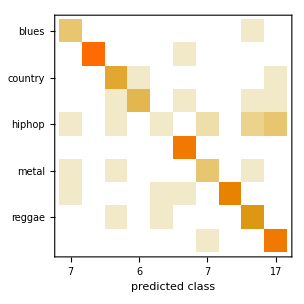
Classifier Measurements
Classifier method | Net
Number of test examples | 100
Accuracy | (72.5.) %
Accuracy baseline | (14.03.5) %
Geometric mean of probabilities | 0.235 ± 0.06
Mean cross entropy | 1.45 ± 0.25
Single evaluation time | 4.46 ms/example
Batch evaluation speed | 961. examples/s
-Graphics- |

0.72

```mathematica
trainednet4=NetTrain[net4,trainSet,ValidationSet->validationSet,MaxTrainingRounds->100]
cl=ClassifierMeasurements[trainednet4,validationSet]
cl["Accuracy"]
```

#### Music Genre Classification Method

```mathematica
findGenre[sound_]:=With[{audio=Values@AudioLocalMeasurements[AudioResample[sound,22050],"MFCC",PartitionGranularity->{1.,1.}]},trainednet4[audio]]
```

```mathematica
findGenre[bluesData[[-3]]]
```

blues

```mathematica
findGenre[reggaeData[[10]]]
```

reggae

## APIs

```mathematica
CloudDeploy[FormPage[{"Music" -> "wav"}, findGenre[#Music] &, AppearanceRules-><|"Title"->"Music Genre Classification","Description"-> Column[{Row[WebImageSearch["music",1]],"Please upload music(.wav) to classify genre", "We have 10 music genre to classify:", "1.blues, 2.classical, 3.country, 4.disco, 5.hiphop, 6.jazz, 7.reggae, 8.rock, 9.metal, and 10.pop"}]|>], "Prediction",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/pakin_kampeera/Prediction]